### NHB paper Figure 2

Simulation results used for Figure 2

```mathematica
figure2=Import["simulation.dat","Table"]
```

{{0.0753733,0.0765239,0.0799299,0.0819262},{0.0769477,0.0774767,0.083137,0.0838066},{0.0776037,0.0787824,0.0855307,0.0859634},{0.0785254,0.0793214,0.0880346,0.0887649},{0.0786626,0.0802713,0.0912171,0.0918712},{0.0776862,0.0816445,0.094842,0.09579},{0.0771956,0.082232,0.0975335,0.103027},{0.076523,0.0827872,0.100495,0.108931},{0.0759441,0.0821759,0.103124,0.115487},{0.0743755,0.0820558,0.106503,0.122819},{0.072161,0.0812759,0.111418,0.133189},{0.0693924,0.0799144,0.117517,0.148184},{0.0669344,0.07815,0.123428,0.166078},{0.0644457,0.0768513,0.130526,0.190992},{0.0630949,0.0753052,0.137285,0.220395},{0.0603227,0.0730477,0.141156,0.259792},{0.0583608,0.0698536,0.145343,0.315194},{0.0561587,0.0661982,0.153847,0.400758},{0.0543745,0.0620492,0.153314,0.513632},{0.0522361,0.0584037,0.152159,0.647419},{0.0509892,0.0564072,0.151629,0.767565},{0.0504301,0.0547033,0.157631,0.853116},{0.0502894,0.0529477,0.160641,0.905263},{0.0501789,0.0527674,0.15926,0.932009},{0.050064,0.0519448,0.153338,0.946477},{0.05,0.051892,0.151424,0.95},{0.0500283,0.0517922,0.141489,0.95},{0.0500836,0.0519801,0.13633,0.95},{0.05,0.0516966,0.126671,0.95},{0.05,0.0513921,0.124371,0.95},{0.0500822,0.0508992,0.12869,0.95},{0.050201,0.051066,0.126069,0.95},{0.0503113,0.0511395,0.116431,0.95},{0.0502824,0.0513302,0.110624,0.95},{0.0502835,0.0510024,0.10872,0.95},{0.0501266,0.050278,0.104053,0.95},{0.0501328,0.0501554,0.0931072,0.95},{0.0502562,0.050543,0.0810077,0.95},{0.0504556,0.0507997,0.0714653,0.95},{0.0502479,0.0503024,0.0675315,0.95},{0.0500991,0.0501824,0.0637322,0.95},{0.0501931,0.0504582,0.0608224,0.95},{0.0502694,0.0504004,0.0591149,0.95},{0.0502731,0.0502985,0.0582347,0.95},{0.0502095,0.0503895,0.0550805,0.95},{0.0503449,0.050425,0.0546,0.95},{0.0502667,0.0508064,0.0534715,0.95},{0.0502575,0.0507131,0.0530074,0.95},{0.0500496,0.0508198,0.0525905,0.95},{0.0503077,0.0507407,0.05286,0.95}}

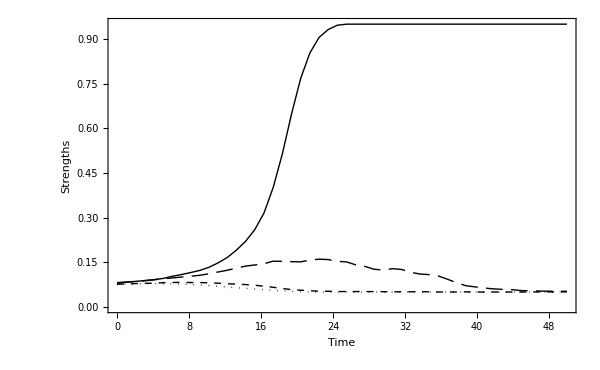

```mathematica
ListPlot[figure2ᵀ,Joined->True,PlotRange-> Full,Frame->True,FrameLabel->{"Time","Strengths"},PlotStyle->{{Dotted,Black},{Dashed,Black},{Dashing[{0.02,0.01}],Black},Black},LabelStyle->Directive[14,FontFamily-> "Times"],DataRange->{0,50},ImageSize->{600,400}]
```